# Polarizzazione Topologica in 1D con OBC

## Spiegazione Teorica

## Parametri

```mathematica
(* parametri *)
charge = 1.0;       (* carica elementare *)
aa          = 10;      (* parametro di reticolo, è pari a due volte la distanza interatomica *)
ϵ            = 1;  (* energia sul sito, positiva per i cationi negativa per gli anioni *)
t            = -1.0 ;     (* energia di hopping *)
```

## Funzioni

```mathematica
(* funzioni *)
(* hamiltoniane *)
(* hamiltoniana con condizioni al contorno aperte (OBC) *)
(* che partono con un catione e finiscono con un anione *)
hamchainOBC[sites_]:=SparseArray[Which[sites==1,{{i_,i_}-> +ϵ},sites==2,{{1,1}-> +ϵ,{2,2}->-ϵ,{1,sites}-> t,{sites,1}->t},sites>2,{{i_?OddQ,i_?OddQ}-> ϵ,{i_?EvenQ,i_?EvenQ}->-ϵ,{i_,j_}/;Or[i==(j+1),i==(j-1),j==(i+1),j==(i-1)]->t}],{sites,sites}];
(* che partono con un anione e finiscono con un catione *)
hamchainOBCinv[sites_]:=SparseArray[Which[sites==1,{{i_,i_}-> -ϵ},sites==2,{{1,1}-> -ϵ,{2,2}->ϵ,{1,sites}-> t,{sites,1}->t},sites>2,{{i_?OddQ,i_?OddQ}->- ϵ,{i_?EvenQ,i_?EvenQ}->ϵ,{i_,j_}/;Or[i==(j+1),i==(j-1),j==(i+1),j==(i-1)]->t}],{sites,sites}];
energy[hamiltoniana_]:=Eigensystem[hamiltoniana][[1]];
vects[hamiltoniana_]:=Eigensystem[hamiltoniana][[2]];
(* costruiamo il ground state selezionando gli autovettori ad energia minima *)
negenergy[hamiltoniana_]:=Select[energy[hamiltoniana],Negative];
negvects[hamiltoniana_]:=Pick[vects[hamiltoniana],Negative[energy[hamiltoniana]]];
(* Costruiamo il ground state *)
groundstate[hamiltoniana_,sites_]:=Sqrt[2]Total[negvects[hamiltoniana]]/Sqrt[sites];

carpos[sites_,hamiltoniana_]:=Inverse[vects[hamiltoniana]]DiagonalMatrix[aa*Range[0,(sites-1),1]] vects[hamiltoniana] ;
polarization[sites_,hamiltoniana_]:=(charge/(2 Pi) )* Im [Log[  Conjugate[groundstate[hamiltoniana,sites]].(  E^(( I * 2 Pi /(sites*aa))( carpos[sites,hamiltoniana]  -2 )).groundstate[hamiltoniana,sites] ) ]] ;
polarization2[sites_,hamiltoniana_]:=(charge/(2sites*aa))* ( Sum[i*aa,{i,0,sites-1}]-(Conjugate[groundstate[hamiltoniana,sites]].  (DiagonalMatrix[aa*Range[0,(sites-1),1]] .groundstate[hamiltoniana,sites]) )) ;
(* definiamo la funzione di distribuzione *)
gauss[α_,ϵ_,e_]:= ( α / π ) Exp[ - α (e-ϵ)^2] (* prima variabile la grandezza, la seconda il valore del centro della gaussiana, e la terza l'ascissa *)
(* Densità di stati *)
dens[α_,ϵ_,energy_,sites_]:= 2/(sites*aa)Total[ gauss[α,ϵ,energy]]
(* hamiltoniana che parte da un catione in cui l'hoping parameter t è variabile *)
hamchainOBCtdep[sites_,t_]:=SparseArray[Which[sites==1,{{i_,i_}-> +ϵ},sites==2,{{1,1}-> +ϵ,{2,2}->-ϵ,{1,sites}-> t,{sites,1}->t},sites>2,{{i_?OddQ,i_?OddQ}-> ϵ,{i_?EvenQ,i_?EvenQ}->-ϵ,{i_,j_}/;Or[i==(j+1),i==(j-1),j==(i+1),j==(i-1)]->t}],{sites,sites}];
(* hamiltoniana in cui l'alternanza anioni e cationi è disordinata, ma l'hopping parameter ha una distribuzione uniforme tra 0 e 1 *)
hamchainOBCdisorder[sites_]:=SparseArray[Which[sites==1,{{i_,i_}-> +RandomReal[{0.5,1}]},sites==2,{{1,1}-> +RandomReal[{0.5,1}],{2,2}->-RandomReal[{0.5,1}],{1,sites}-> t,{sites,1}->t},sites>2,{{i_?OddQ,i_?OddQ}->RandomReal[{0.5,1}],{i_?EvenQ,i_?EvenQ}->-RandomReal[{0.5,1}],{i_,j_}/;Or[i==(j+1),i==(j-1),j==(i+1),j==(i-1)]->t}],{sites,sites}];
```

```mathematica
(groundstate[hamchainOBC[100],100]).groundstate[hamchainOBC[100],100]
```

1.

```mathematica
(* spazio reciproco, orbitali di bloch *)
```

```mathematica
(* Discrete Fourier Transform of each eigenstate to obtain κ quantum number *)
κvals[vects_]:=Map[Flatten[Position[Abs[Chop[Fourier[#]]],Except[0,_?NumberQ]]-1]&,vects,1]; 
(* k-points inside the reduced BZ, k-points are periodic in 2π/a, i.e -π/a goes into π/a *) (*extra: from 0 to 2 π / a*)
κvalsred[κvals_,sites_]:=ReplacePart[κvals,{i_,j_}:> κvals[[i,j]]-sites];
kpts[κvalsred_,sites_]:=Map[2*Pi*#/(sites*aa)&,κvalsred,1];
data[κvals_,κvalsred_,kpts_,energy_]:=Transpose[{κvals,κvalsred,kpts,energy}];
(* changing default options for frameticks in MatrixPlot *)
κlist[sites_]:=Table[κ,{κ,0,sites-1,1}];
indexframehoriz[sites_]:=Table[s,{s,1,sites,1}];
dataframe[κlist_,indexframehoriz_]:=Transpose[{indexframehoriz,κlist}];
(*Brillouin zone construction *)
bzextrema={{-π/aa,0},{π/aa,0}};
ybzcoord[kpts_]:=Table[0,{Length[Flatten[kpts]]}];
bzkpts[kpts_,ybzcoord_]:=Transpose[{Flatten[kpts],ybzcoord}];
lineampi={Thick,Black,Line[{{-π/aa,-0.2},{-π/aa,0.2}}]};
lineampitxt=Text[Style["-\!\(\*FractionBox[\"π\", \"a\"]\)",16,Bold],{-π/aa,-0.9}];
lineappi={Thick,Black,Line[{{π/aa,-0.2},{π/aa,0.2}}]};
lineappitxt=Text[Style["\!\(\*FractionBox[\"2π\", \"a\"]\)",16,Bold],{π/aa,-0.9}];
lineazerobz={Thick,Black,Line[{{Pi/aa,-0.2},{Pi/aa,0.2}}]}; (* cambiato 16-07-19 prima era {{0,-0.2},{0,0.2}} *)
lineazerobztxt=Text[Style["0",16,Bold],{0,-0.9}];
labelbztxt=Text[Style["k",16,Italic,Bold],{0,-1.9}];
titlebztxt=Text[Style["First Brillouin Zone",14,Bold],{0,1.6}];
```

## Grafici

```mathematica
Manipulate[Column[{
Text[Style["Hamiltonian Matrix and Discrete Fourier Transform Intensity Pattern",Black,Bold,14]],Grid[{{Column[{MatrixPlot[hamchainOBC[sites],Mesh->All,ImageSize->{175,175}],Show[{Plot[{Sqrt[ϵ^2+(2t*Cos[kappa*aa/2])^2],-Sqrt[ϵ^2+(2t*Cos[kappa*aa/2])^2]},{kappa,-π/(aa),π/(aa)}],{ListPlot[Transpose[{Flatten[DeleteDuplicates[kpts[κvalsred[κvals[vects[hamchainOBC[sites]]],sites],sites]]],Flatten[energy[hamchainOBC[sites]]
]}],PlotStyle->{PointSize[0.03],Green}]}},Frame->True,PlotRange->{-10.,10.},FrameTicks->{{{-10,-5,0,5,10},None},{{{-π/aa,"-π/aa"},{Pi/(2*(aa)),"-π/2a"},0,{Pi/((2aa)),"π/2a"},{3Pi/(2*(aa)),"3π/2a"},{2 Pi/(aa),"2π/a"}},None}},FrameLabel->{{Text[Style["Energy (eV)",Black,Bold,12]],""},{Text[Style["k",Black,Bold,Italic,14]],Text[Style["Electronic Dispersion Relation",Black,Bold,14]]}},ImageSize->{220,220}]},Center],Column[{Show[{MatrixPlot[Map[Flatten[Abs[Chop[Fourier[#]]]]&,vects[hamchainOBC[sites]],1],Mesh->All,ImageSize->{200,200},Frame->True,FrameTicks->{{Automatic,None},{dataframe[κlist[sites],indexframehoriz[sites]],None}},FrameLabel->{"","",Text[Style["Eigenvectors",Black,11]],Text[Style["κ",Black,14]]}]}],
Show[{Graphics[{Thick,Black,Line[bzextrema],lineampi,lineampitxt,lineappi,lineappitxt,lineazerobz,lineazerobztxt,labelbztxt,titlebztxt,PointSize[0.03],Green,Point[bzkpts[kpts[κvalsred[κvals[vects[hamchainOBC[sites]]],sites],sites],ybzcoord[kpts[κvalsred[κvals[vects[hamchainOBC[sites]]],sites],sites]]]]}]},ImageSize->{190,190}]}]}}]},Center],{{sites,2,"N sites"},2,100,2,Appearance->"Labeled"},TrackedSymbols:>{sites}]
```

Transpose::nmtx: The first two levels of {kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«21»,«16»,«20»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],18],18],{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«21»,«16»,«20»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],«7»],«7»],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«21»,«16»,«20»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],18.],«4»],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«1»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],18.],«4»],«1»}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

Transpose::nmtx: The first two levels of {kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«21»,«16»,«20»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],18],18],{«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of {kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«21»,«16»,«20»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],«7»],«7»],«1»} cannot be transposed.

Transpose::nmtx: The first two levels of {kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«21»,«16»,«20»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],18.],«4»],«1»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{kpts[κvalsred[κvals[{{0.0643514,-0.0779748,0.186081,-0.1475,0.287645,-0.201041,0.358039,-0.232796,0.389634,-0.239324,0.379006,-0.219918,0.327306,-0.17668,0.240138,-0.114296,0.126947,-0.0395265},{«1»},«15»,{0.455734,-0.0061738,-0.443303,0.0121792,0.418779,-0.0178524,-0.382833,«4»,0.0314014,0.217649,-0.0343498,-0.148484,0.0363613,0.0752684,-0.037381}}],18.],«4»],«1»}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
sites=6
```

6

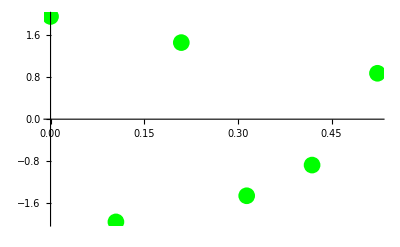

```mathematica
ListPlot[Transpose[{Flatten[DeleteDuplicates[kpts[κvals[vects[hamchainOBC[sites]]],sites]]],Flatten[energy[hamchainOBC[sites]]
]}],PlotStyle->{PointSize[0.03],Green}]
```

```mathematica
Flatten[kpts[κvals[vects[hamchainOBC[sites]]],sites],sites]
```

{0,π/30,π/15,π/10,(2 π)/15,π/6,0,π/30,π/15,π/10,(2 π)/15,π/6,0,π/30,π/15,π/10,(2 π)/15,π/6,0,π/30,π/15,π/10,(2 π)/15,π/6,0,π/30,π/15,π/10,(2 π)/15,π/6,0,π/30,π/15,π/10,(2 π)/15,π/6}

```mathematica
kpts[κvalsred[κvals[vects[hamchainOBC[sites]]],sites],sites]
```

{{0,-π/6,π/15,-π/10,(2 π)/15,-π/30},{0,-π/6,π/15,-π/10,(2 π)/15,-π/30},{0,-π/6,π/15,-π/10,(2 π)/15,-π/30},{0,-π/6,π/15,-π/10,(2 π)/15,-π/30},{0,-π/6,π/15,-π/10,(2 π)/15,-π/30},{0,-π/6,π/15,-π/10,(2 π)/15,-π/30}}

```mathematica
κvalsred[κvals[vects[hamchainOBC[sites]]],sites]
```

{{0,-5,2,3,4,5},{0,-5,2,3,4,5},{0,-5,2,3,4,5},{0,-5,2,3,4,5},{0,-5,2,3,4,5},{0,-5,2,3,4,5}}

```mathematica
κvals[vects[hamchainOBC[sites]]]
```

{{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5}}

```mathematica
vects[hamchainOBC[sites]]
```

{{0.272866,-0.327927,0.613123,-0.408918,0.491687,-0.181986},{0.181986,0.491687,0.408918,0.613123,0.327927,0.272866},{-0.514451,0.362765,-0.285499,-0.161446,0.64151,-0.290915},{0.290915,0.64151,0.161446,-0.285499,-0.362765,-0.514451},{0.194992,0.316297,-0.156371,-0.569947,0.0867796,0.710712},{0.710712,-0.0867796,-0.569947,0.156371,0.316297,-0.194992}}

```mathematica
κvals[vects[hamchainOBC[sites]]]
```

{{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5}}

```mathematica
Map[Flatten[Position[Abs[Chop[Fourier[#]]],Except[0,_?NumberQ]]-1]&,vects[hamchainOBC[sites]],1]
```

{{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5}}

```mathematica
Map[Flatten[Position[Chop[Fourier[#]],Except[0,_?NumberQ]]-1]&,vects[hamchainOBC[sites]],1]
```

{{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5},{0,1,2,3,4,5}}

## Computazioni

### Caso Ordinato

```mathematica
Manipulate[ListPlot[Table[polarization2[i,hamchainOBCtdep[i,τ]]/(0.5*i),{i,2,100,2}],AxesOrigin->{0,0},Frame->True,FrameLabel->{Style["Numero di Celle Unitarie",Large],Style["Polarizzazione per unità di Cella",Large]}],{{τ,0,"t"},0,-1,-0.1,Appearance->"Labeled"},TrackedSymbols:>{τ}]
```

```mathematica
Manipulate[ListPlot[Table[Log[polarization2[i,hamchainOBCtdep[i,τ]]/(0.5*i)],{i,2,100,2}],AxesOrigin->{0,0},Frame->True,FrameLabel->{Style["Numero di Celle Unitarie",Large],Style["Polarizzazione per unità di Cella",Large]}],{{τ,0,"t"},0,-1,-0.1,Appearance->"Labeled"},TrackedSymbols:>{τ}]
```

Ci interessa andare a vedere l’andamento per cui converge la polarizzazione. Facciamo quind un grafico log-log e andiamo ad analizzare il coefficiente angolare per capirlo.

```mathematica
logpolarization[τ_]:=Table[{Log[i],Log[polarization2[i,hamchainOBCtdep[i,τ]]/(0.5*i)]},{i,2,100,2}];
```

```mathematica
logpolarization[-1]
```

{{Log[2],Indeterminate},{Log[4],-2.26493+3.14159 ⅈ},{Log[6],-1.39098+3.14159 ⅈ},{Log[8],-0.899329+3.14159 ⅈ},{Log[10],-0.561353+3.14159 ⅈ},{Log[12],-0.305231+3.14159 ⅈ},{Log[14],-0.0996157+3.14159 ⅈ},{Log[16],0.0718654+3.14159 ⅈ},{Log[18],0.218794+3.14159 ⅈ},{Log[20],0.347245+3.14159 ⅈ},{Log[22],0.4613+3.14159 ⅈ},{Log[24],0.563833+3.14159 ⅈ},{Log[26],0.65694+3.14159 ⅈ},{Log[28],0.742197+3.14159 ⅈ},{Log[30],0.820814+3.14159 ⅈ},{Log[32],0.893745+3.14159 ⅈ},{Log[34],0.961756+3.14159 ⅈ},{Log[36],1.02546+3.14159 ⅈ},{Log[38],1.08537+3.14159 ⅈ},{Log[40],1.1423+3.14159 ⅈ},{Log[42],1.23378+3.14159 ⅈ},{Log[44],1.24627+3.14159 ⅈ},{Log[46],6.24842+3.14159 ⅈ},{Log[48],1.67355+3.14159 ⅈ},{Log[50],1.38492+3.14159 ⅈ},{Log[52],14.9917+3.14159 ⅈ},{Log[54],1.51392+3.14159 ⅈ},{Log[56],1.50593+3.14159 ⅈ},{Log[58],30.0021+3.14159 ⅈ},{Log[60],33.1316+3.14159 ⅈ},{Log[62],1.61586+3.14159 ⅈ},{Log[64],13.8663+3.14159 ⅈ},{Log[66],47.4728+3.14159 ⅈ},{Log[68],6.31559+3.14159 ⅈ},{Log[70],54.9958+3.14159 ⅈ},{Log[72],56.6694+3.14159 ⅈ},{Log[74],1.80602+3.14159 ⅈ},{Log[76],38.5877+3.14159 ⅈ},{Log[78],72.2799+3.14159 ⅈ},{Log[80],23.3796+3.14159 ⅈ},{Log[82],77.6088+3.14159 ⅈ},{Log[84],46.0962+3.14159 ⅈ},{Log[86],31.2902+3.14159 ⅈ},{Log[88],91.4681+3.14159 ⅈ},{Log[90],65.8998+3.14159 ⅈ},{Log[92],39.1116+3.14159 ⅈ},{Log[94],64.1389+3.14159 ⅈ},{Log[96],103.223+3.14159 ⅈ},{Log[98],37.1451+3.14159 ⅈ},{Log[100],116.578+3.14159 ⅈ}}

```mathematica
LinearModelFit[logpolarization[1],{1,x},x]
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{Log[2],Indeterminate},{Log[4],-2.26493+3.14159 ⅈ},{Log[6],-1.39098+3.14159 ⅈ},{Log[8],-0.899329+3.14159 ⅈ},{Log[10],-0.561353+3.14159 ⅈ},{Log[12],-0.305231+3.14159 ⅈ},{Log[14],-0.0996157+3.14159 ⅈ},{Log[16],0.0718654+3.14159 ⅈ},{Log[18],0.218794+3.14159 ⅈ},{Log[20],0.347245+3.14159 ⅈ},{Log[22],0.4613+3.14159 ⅈ},{Log[24],0.563833+3.14159 ⅈ},{Log[26],0.65694+3.14159 ⅈ},{Log[28],0.742196+3.14159 ⅈ},{Log[30],0.820813+3.14159 ⅈ},{Log[32],0.893745+3.14159 ⅈ},{Log[34],0.961756+3.14159 ⅈ},{Log[36],1.02546+3.14159 ⅈ},{Log[38],1.08537+3.14159 ⅈ},{Log[40],1.1423+3.14159 ⅈ},{Log[42],1.23378+3.14159 ⅈ},{Log[44],1.24627+3.14159 ⅈ},{Log[46],6.24842+3.14159 ⅈ},{Log[48],1.67355+3.14159 ⅈ},{Log[50],1.38492+3.14159 ⅈ},{Log[52],16.0671+3.14159 ⅈ},{Log[54],1.51392+3.14159 ⅈ},{Log[56],1.50593+3.14159 ⅈ},{Log[58],29.9872+3.14159 ⅈ},{Log[60],33.9385+3.14159 ⅈ},{Log[62],1.61584+3.14159 ⅈ},{Log[64],13.8663+3.14159 ⅈ},{Log[66],47.4332+3.14159 ⅈ},{Log[68],6.31241+3.14159 ⅈ},{Log[70],55.2484+3.14159 ⅈ},{Log[72],56.6763+3.14159 ⅈ},{Log[74],1.80602+3.14159 ⅈ},{Log[76],38.0113+3.14159 ⅈ},{Log[78],72.2799+3.14159 ⅈ},{Log[80],24.0346+3.14159 ⅈ},{Log[82],77.6088+3.14159 ⅈ},{Log[84],46.1515+3.14159 ⅈ},{Log[86],30.5425+3.14159 ⅈ},{Log[88],91.4681+3.14159 ⅈ},{Log[90],65.8998+3.14159 ⅈ},{Log[92],39.1116+3.14159 ⅈ},{Log[94],64.1389+3.14159 ⅈ},{Log[96],103.223+3.14159 ⅈ},{Log[98],37.5686+3.14159 ⅈ},{Log[100],116.578+3.14159 ⅈ}},{1,x},x]

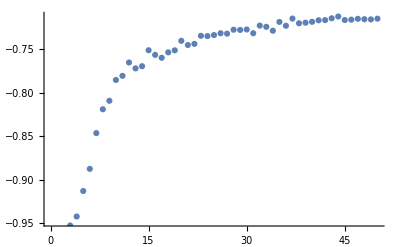

```mathematica
Table[LinearModelFit[logpolarization[tau],{1,x},x],{tau,-2,-1,0.2}]
```

### Caso Disordinato

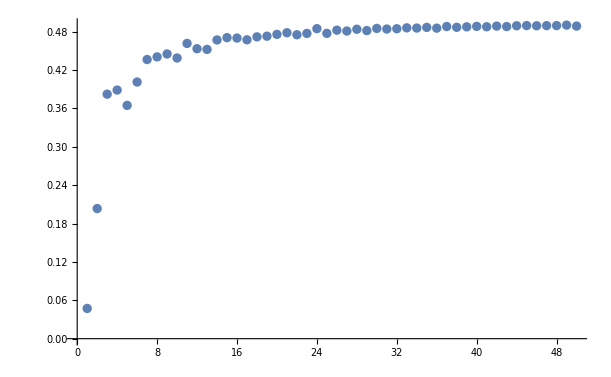

```mathematica
ListPlot[Table[polarization2[i,hamchainOBCdisorder[i]]/(0.5*i),{i,2,100,2}],AxesOrigin->{0,0}]
```

## Densità di Stati

Calcoliamo la densità di stati nel caso di condizioni al contorno aperte, nel caso ordinato e disordinato e vediamo se sono simili. Dopodiché nel caso di condizioni al contorno periodiche. Definiamo la densità dei livelli nella banda n-esima come:
g(ϵ) = 2∫_BZ dk δ( ϵ - ϵ_nk) 
Nel nostro caso, abbiamo un sistema con due bande, e consideriamo il caso half filling con coppie di elettroni spinless solo nella banda ad energia inferiore.
La densità di stati in un volume V e con N livelli di energia (countable) è definita da:
D(ϵ)= 1/L∑_k δ( ϵ-ϵ_k)
Regolarizziamo questa funzione rimpiazzando la funzione δ con una funzione gaussiana rinormalizzata della forma:
G_α( ϵ-ϵ_nk) = √α/π e^(-α ( ϵ-ϵ_nk)^2)
Questa sostituzione va bene per larghezze gaussiane più grandi dello spacing tra livelli di energia tali che
lim_(α→ ∞) G_α(x-x_0)=δ(x_0)

Andiamo a vedere la densità di stati per t=0 (ho una hamiltoniana già diagonale)

```mathematica
Manipulate[{dos=Total[gauss[α,energy[hamchainOBCtdep[sites,t]],x]]/sites;Plot[dos,{x,-5,5},ImageSize->{400,400}]},{{sites,2,"N"},2,100,2,Appearance->"Labeled"},{{α,2,"α"},1,50,1,Appearance->"Labeled"},{{t,0,"t"},0,-1,-0.01,Appearance->"Labeled"},TrackedSymbols:>{sites,α,t}]
```

General::munfl: Exp[-712.378] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.893] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.56517×10^-308 0.31831 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-712.378] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.893] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.56517×10^-308 0.31831 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
plot1=Table[{t,x,Total[gauss[10,energy[hamchainOBCtdep[100,t]],x]]/100},{t,0,-1,-0.01},{x,-4,4,0.1}];
```

```mathematica
ListPlot3D[Partition[Flatten[plot1],3],BoxRatios->{1, 1, 1},AxesLabel->{"t","energy","dos"}]/.Point[a___]:>{Thick,Line[a]}
```

-Graphics3D-

## Caso Disordinato

```mathematica
hamchainOBCdisorder[sites_]:=SparseArray[Which[sites==1,{{i_,i_}-> +RandomReal[{0.5,1}]},sites==2,{{1,1}-> +RandomReal[{0.5,1}],{2,2}->-RandomReal[{0.5,1}],{1,sites}-> t,{sites,1}->t},sites>2,{{i_?OddQ,i_?OddQ}->RandomReal[{0.5,1}],{i_?EvenQ,i_?EvenQ}->-RandomReal[{0.5,1}],{i_,j_}/;Or[i==(j+1),i==(j-1),j==(i+1),j==(i-1)]->t}],{sites,sites}]
```

```mathematica
Manipulate[{dos=Total[gauss[α,energy[hamchainOBCdisorder[sites]],x]];Plot[dos,{x,-5,5},ImageSize->{400,400}]},{{α,2,"α"},1,50,1,Appearance->"Labeled"},{{sites,2,"sites"},2,200,2,Appearance->"Labeled"},TrackedSymbols:>{α,sites}]
```

General::munfl: Exp[-2406.79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2404.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2400.65] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2524.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2522.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2518.21] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-2552.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2549.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2545.97] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Eigensystem::arh: Because finding 142 out of the 142 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::munfl: Exp[-2482.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2481.09] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2479.49] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Eigensystem::arh: Because finding 142 out of the 142 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
plot2=Table[{sites,x,Total[gauss[10,energy[hamchainOBCdisorder[sites]],x]]},{sites,2,200,2},{x,-4,4,0.1}];
```

Eigensystem::arh: Because finding 102 out of the 102 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

```mathematica
ListPlot3D[Partition[Flatten[plot2],3],BoxRatios->{1, 1, 1},AxesLabel->{"sites","energy","dos"}]/.Point[a___]:>{Thick,Line[a]}
```

-Graphics3D-

## Polarizzazione

We will define the macroscopic polarization as:
P=e/2∫ⅆx(n_at(x)-n_el(x))
where n_at(x) is the atomic density and n_el(x) is the electron density. 
For n_at(x) we choose to localize in the atomic position x_i
n_at(x)=1/N ∑_i δ(x-x_i)
whereas the electron density:
n_el(x)= 1/N∑_(lowest eigenvectors) ψ_k(x)

```mathematica
PolarizzazioneOBC[ ]:= (charge/2 ) NIntegrate[gauss[0.1,x,,{x,-10,10}]
```